```mathematica
kb=1/t0 Exp[(-μ k)/(2 d)dl^2 Sqrt[1+4 μ k τ]]/.{t0->(π η)/(μ k)}/.{η->1+2 μ k τ}//FullSimplify;
```

```mathematica
kb
```

```mathematica
(1/kb)/.{d->100,τ->0.5,k->1/(r μ)}/.{r->0.25}
```

```mathematica
3.9269908169872414 ⅇ^(0.06 dl^2)/.{dl->5}
```

17.5996

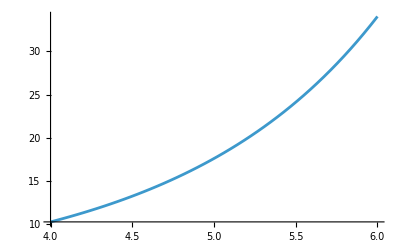

```mathematica
Plot[3.9269908169872414 ⅇ^(0.06 dl^2),{dl,4,6}]
```